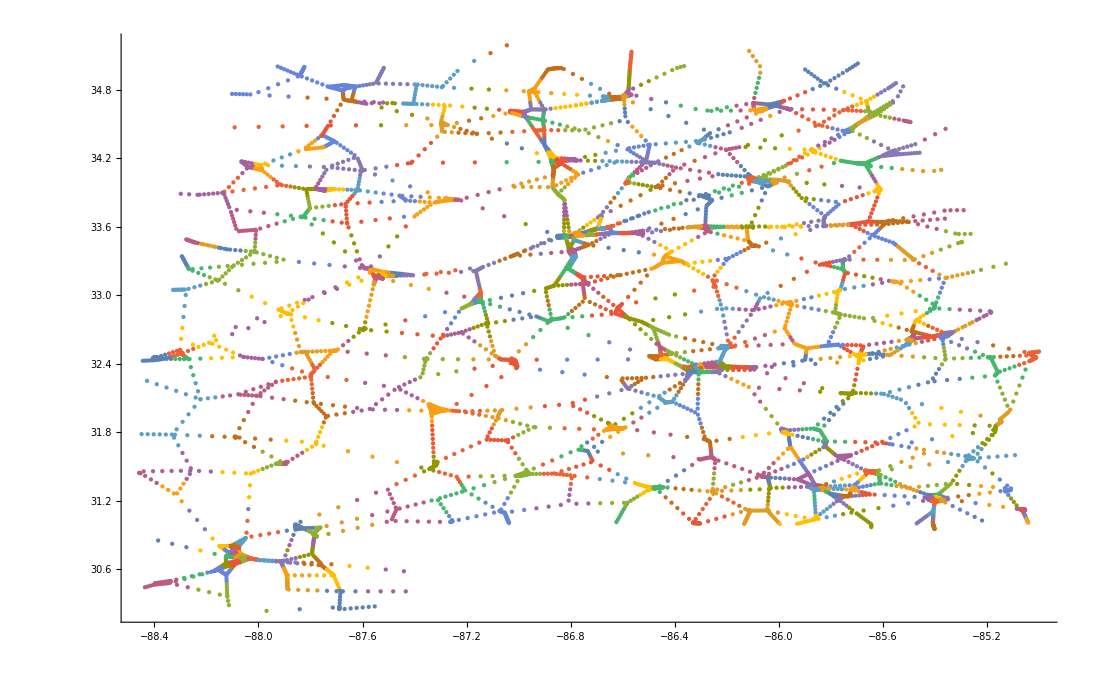

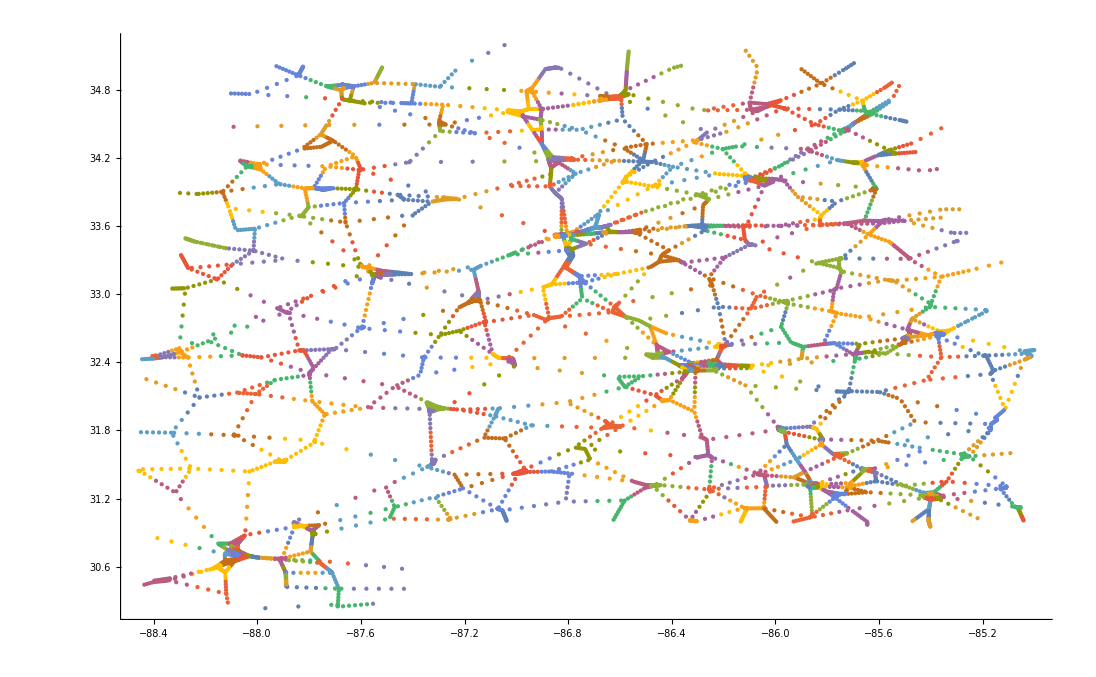

```mathematica
datapairs = ReadList["~/Desktop/test_point_AL.txt",{Number,Number}];

ListPlot[FindClusters[datapairs,2800,Method->"KMeans"]]
ListPlot[FindClusters[datapairs,2800,Method->"KMedoids"]]
```